```mathematica
p[x_]=a*x+b
```

b+a x

```mathematica
nodes = {{2,4},{4,5},{6,6},{7,7},{10,8},{11,8},{14,11},{17,10},{20,12}}
```

{{2,4},{4,5},{6,6},{7,7},{10,8},{11,8},{14,11},{17,10},{20,12}}

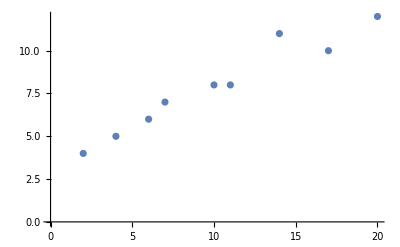

```mathematica
points=ListPlot[nodes]
```

```mathematica
kvadrati[a_,b_]=Sum[(nodes[[i,2]] - p[nodes[[i,1]]])^2,{i,Length[nodes]}]
```

(12-20 a-b)^2+(10-17 a-b)^2+(11-14 a-b)^2+(8-11 a-b)^2+(8-10 a-b)^2+(7-7 a-b)^2+(6-6 a-b)^2+(5-4 a-b)^2+(4-2 a-b)^2

```mathematica
sol=NSolve[{D[kvadrati[a,b],a]==0,D[kvadrati[a,b],b]==0},{a,b}]
```

{{a→0.436975,b→3.47059}}

```mathematica
F[x_]=p[x]/.sol[[1]]
```

3.47059+0.436975 x

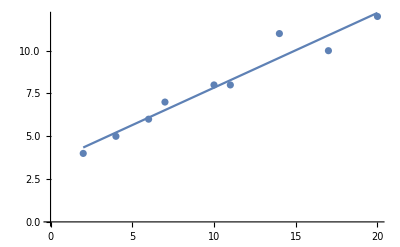

```mathematica
Show[points,Plot[F[x],{x,2,20}]]
```